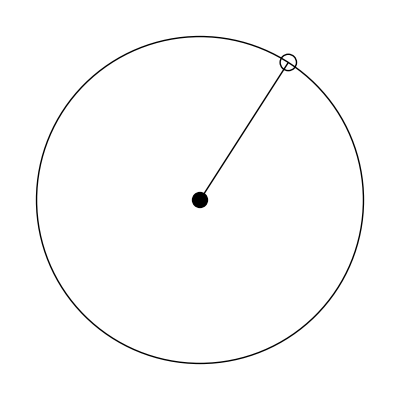

```mathematica
Graphics[{
Circle[{0, 0}, 1],
Disk[{0, 0}, 0.05],
Circle[{Cos[1], Sin[1]}, 0.05],
Line[{{0, 0}, {Cos[1], Sin[1]}}]
}]
```

```mathematica
Manipulate[
GraphicsGrid[{
{
Graphics[{
Circle[{0, 0}, 1],
Disk[{0, 0}, 0.05],
Circle[{Cos[t], Sin[t]}, 0.05],
Line[{{0, 0}, {Cos[t], Sin[t]}}]
}, PlotRange->{{-1.1, 1.1}, {-1.1, 1.1}}],
Plot[Sin[x], {x, 0, t}, PlotRange->{{0, 8Pi}, {-1.1, 1.1}}]
}
}],
{t, 0.001, 8Pi}]
```

```mathematica
Manipulate[
GraphicsGrid[{
{
Graphics[{
Circle[{0, 0}, 1],
Disk[{0, 0}, 0.05],
Circle[{Cos[t], Sin[t]}, 0.05],
Line[{{0, 0}, {Cos[t], Sin[t]}}]
}, PlotRange->{{-1.1, 1.1}, {-1.1, 1.1}}],
Plot[Sin[x], {x, 0, t}, PlotRange->{{0, 8Pi}, {-1.1, 1.1}}]
},{
Plot[Cos[x], {x, 0, t}, PlotRange->{{0, 8Pi}, {-1.1, 1.1}}]
}
}],
{t, 0.001, 8Pi}]
```

```mathematica
?Rotate
```

Rotate[g,θ] represents 2D graphics primitives or any other objects g rotated counterclockwise by θ radians about the center of their bounding box. 
Rotate[g,θ,{x,y}] rotates about the point {x,y}. 
Rotate[g,{u,v}] rotates around the origin, transforming the 2D or 3D vector u to v.
Rotate[g,θ,w] rotates 3D graphics primitives by θ radians around the 3D vector w anchored at the origin.
Rotate[g,θ,w,p] rotates around the 3D vector w anchored at p.
Rotate[g,θ,{u,v}] rotates by angle θ in the plane spanned by 3D vectors u and v.

```mathematica
Manipulate[
GraphicsGrid[{
{
Graphics[{
Circle[{0, 0}, 1],
Disk[{0, 0}, 0.05],
Circle[{Cos[t], Sin[t]}, 0.05],
Line[{{0, 0}, {Cos[t], Sin[t]}}]
}, PlotRange->{{-1.1, 1.1}, {-1.1, 1.1}}, AspectRatio->1],
Plot[Sin[x], {x, 0, t}, PlotRange->{{0, 8Pi}, {-1.1, 1.1}}, AspectRatio->1]
},{
Rotate[Plot[Cos[x], {x, 0, t}, PlotRange->{{0, 8Pi}, {-1.1, 1.1}}, AspectRatio->1], -Pi/2]
}
}],
{t, 0.001, 8Pi}]
```

## Pendulum Project

```mathematica
Theta[t_, theta0_, thetad0_, l_, b_] := 
With[{
wd = Sqrt[-b^2+4×9.81/l]/2
},
Exp[-b/2 t](theta0 Cos[wd t]+(thetad0+b/2 theta0)/wd Sin[wd t])
];
```

```mathematica
Thetad[t_, theta0_, thetad0_, l_, b_]:=
With[{
wd = Sqrt[b^2+4×9.81/l]/2,
A = theta0,
B = (thetad0+b/2 theta0)/(Sqrt[-b^2+4×9.81/l]/2)
},
Exp[-b/2 t]((B wd - A b/2)Cos[wd t]-(b/2 B + A wd)Sin[wd t])
];
```

```mathematica
t = 1;
theta0 = Pi/6;
thetad0 = 1;
l = 1;
b = 0;
```

```mathematica
Theta[t, theta0, thetad0, l, b]
```

0.523599

```mathematica
Pi/6//N
```

0.523599

```mathematica
Thetad[t, theta0, thetad0, l, b]
```

1.

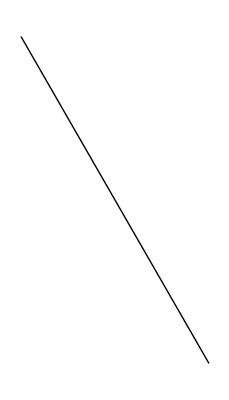

```mathematica
GraphicsGrid[{
{
Graphics[{
Line[{{0, 0}, {1Sin[Theta[t, theta0, thetad0, l, b]], -1Cos[Theta[t, theta0, thetad0, l, b]]}}]
}]
}
}]
```

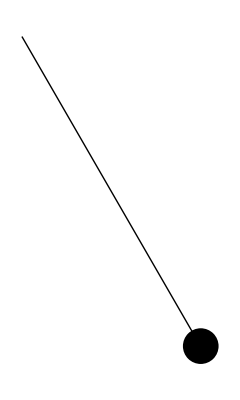

```mathematica
GraphicsGrid[{
{
Graphics[{
Line[{{0, 0}, {1Sin[Theta[t, theta0, thetad0, l, b]], -1Cos[Theta[t, theta0, thetad0, l, b]]}}],
Disk[{1Sin[Theta[t, theta0, thetad0, l, b]], -1Cos[Theta[t, theta0, thetad0, l, b]]}, 0.05]
}]
}
}]
```

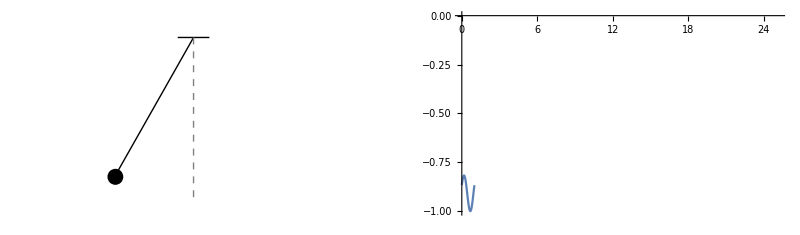

```mathematica
GraphicsGrid[{
{
Graphics[{
Line[{{0, 0}, {1Sin[Theta[t, theta0, thetad0, l, b]], -1Cos[Theta[t, theta0, thetad0, l, b]]}}],
Disk[{1Sin[Theta[t, theta0, thetad0, l, b]], -1Cos[Theta[t, theta0, thetad0, l, b]]}, 0.05],
Line[{{-0.1, 0}, {0.1, 0}}],
{Gray, Dashed, Line[{{0, 0}, {0, -1}}]}
}, PlotRange->{{-1, 1}, {-1.1, .1}}],
Plot[-1Cos[Theta[s, theta0, thetad0, l, b]], {s, 0, t}, PlotRange->{{0, 8Pi}, {-1, 0}}]
}
}]
```

```mathematica
GraphicsGrid[{
{

Graphics[
{
Line[{{0, 0}, {1Sin[Theta[t, theta0, thetad0, l, b]], -1Cos[Theta[t, theta0, thetad0, l, b]]}}],
Disk[{1Sin[Theta[t, theta0, thetad0, l, b]], -1Cos[Theta[t, theta0, thetad0, l, b]]}, 0.05],
Line[{{-0.1, 0}, {0.1, 0}}],{Gray, Dashed, Line[{{0, 0}, {0, -1}}]}
}, PlotRange->{{-1, 1}, {-1.1, .1}}
],
Plot[-1Cos[Theta[s, theta0, thetad0, l, b]], {s, 0, t}, PlotRange->{{0, 8Pi}, {-1, 0}}]
},

{
Rotate[Plot[1Sin[Theta[s, theta0, thetad0, l, b]], {s, 0, t}, PlotRange->{{0, 8Pi}, {-1, 1}}], -Pi/2],
ParametricPlot[{Theta[s, theta0, thetad0, l, b], Thetad[s, theta0, thetad0, l, b]}, {s, 0, t}, PlotRange->{{-2, 2}, {-3, 3}}]
}
}]
```

-Graphics-

```mathematica
Manipulate[

GraphicsGrid[{
{

Graphics[
{
Line[{{0, 0}, {1Sin[Theta[t, theta0, thetad0, l, b]], -1Cos[Theta[t, theta0, thetad0, l, b]]}}],
Disk[{1Sin[Theta[t, theta0, thetad0, l, b]], -1Cos[Theta[t, theta0, thetad0, l, b]]}, 0.05],
Line[{{-0.1, 0}, {0.1, 0}}],{Gray, Dashed, Line[{{0, 0}, {0, -1}}]}
}, PlotRange->{{-1, 1}, {-1.1, .1}}
],
Plot[-1Cos[Theta[s, theta0, thetad0, l, b]], {s, 0, t}, PlotRange->{{0, 8Pi}, {-1, 0}}]
},

{
Rotate[Plot[1Sin[Theta[s, theta0, thetad0, l, b]], {s, 0, t}, PlotRange->{{0, 8Pi}, {-1, 1}}], -Pi/2],
ParametricPlot[{Theta[s, theta0, thetad0, l, b], Thetad[s, theta0, thetad0, l, b]}, {s, 0, t}, PlotRange->{{-2, 2}, {-3, 3}}]
}
}],

{{t, 0.01, "Time"}, 0.01, 8Pi, 0.01},
{{theta0, Pi/6, "Initial Displacement"}, -Pi/4, Pi/4, 0.05},
{{thetad0, 0, "Initial Velocity"}, -1, 1, 0.05},
{{l, 0.9, "Length"}, 0.5, 1},
{{b, 0.1, "Damping Coefficient"}, {0, 0.1, 0.3, 0.6}}
]
```